### Lattice-statics GFs for ZrC

```mathematica
(*hessian.cvac.rear hessian.fren129 hessian.fren142 hessian.perf hessian.zvac*)
```

This note book is about lattice GFs for 2x2x2 supercell of ZrC. Consider perfect Zr32C32, with C vacancy Zr32C31, Zr vacancy, and two types of Frenkel defects.

```mathematica
inputFiles={"hessian.perf","hessian.cvac.rear","hessian.zvac","hessian.fren129","hessian.fren142"};
listZrChessians=Table[ReadList[StringJoin["/Volumes/MicroSD/2_PostDoc_SD/GreensFunctionZrC/Hessian_ZrC_4685Ang_700eV_666kp_2x2x2/",ToString@inputFiles[[i]]],Number],{i,1,Length@inputFiles}];
```

```mathematica
Table[{"Size of ",inputFiles[[i]],listZrChessians[[i]]//Length},{i,1,Length@inputFiles}]//TableForm
threeNatomsForHessians=Table[Sqrt[listZrChessians[[i]]//Length],{i,1,Length@inputFiles}]
```

Size of  | hessian.perf | 36864
Size of  | hessian.cvac.rear | 35721
Size of  | hessian.zvac | 35721
Size of  | hessian.fren129 | 36864
Size of  | hessian.fren142 | 36864

{192,189,189,192,192}

```mathematica
threeNbythreeNhessians=Table[Partition[listZrChessians[[i]],threeNatomsForHessians[[i]]],{i,1,Length@inputFiles}];
```

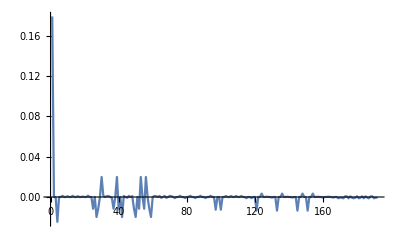

```mathematica
(*Visualise row in Hessian*)
ListLinePlot[threeNbythreeNhessians[[1]][[1]],PlotRange->All]
```

```mathematica
threeNbythreeNhessians[[1]][[1]];
(*Check force constant sum rule is obeyed - each row in Hessian should sum to zero*)
Total@threeNbythreeNhessians[[1]][[1]]
```

2.77556×10^-17

```mathematica
(*https://en.wikipedia.org/wiki/Multiscale_Green%27s_function*)
(*http://ws680.nist.gov/publication/get_pdf.cfm?pub_id=851303*)
```

Dyson equation:
G* = G + GpG* = G + GpG + GpGpG + ...
where  G=H^-1
and p=H-H*

H = perfect Hessian
H* = defective Hessian
G = perfect Greens function

For an initial example, lets consider the perfect 2x2x2 ZrC supercell Hessian, and defective version with the same number of atoms but containing the bound-pair Frenkel defect “hessian.fren129”:

```mathematica
(*Pefect and defective Hessians*)
Hperf=threeNbythreeNhessians[[1]];
HdefStar=threeNbythreeNhessians[[1]];
```

```mathematica
Gperf=Inverse[Hperf];
GdefStar=Inverse[HdefStar];
p=Hperf-HdefStar;
```

```mathematica
(*Sanity check*)
Gperf.Hperf//MatrixForm;
```

```mathematica
(*Check Dyson equation obeyed*)
GdefStar==Gperf+Gperf.p.GdefStar
```

True